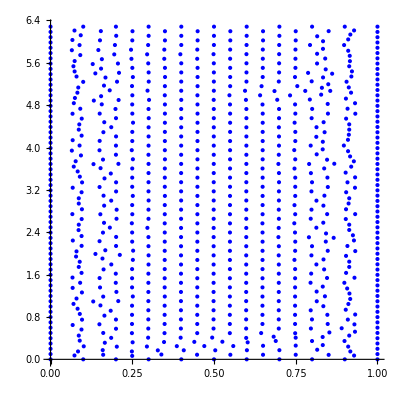

827

```mathematica
tabve=Import["/Users/michelecastellana/Documents/finite_elements/generate_mesh/2d/square_no_circle/solution/vertices.csv"]
tabve=Table[{tabve[[i,1]],tabve[[i,2]]},{i,2,Length[tabve]}]
ListPlot[tabve,PlotStyle->Blue,AspectRatio->1]
Length[tabve]
```

```mathematica
(*write ψ from ODE to csv file*)
```

```mathematica
tabψ=Table[{
ψ[s]/.sol/.{s->tabve[[i,1]]},
tabve[[i,1]],tabve[[i,2]],0},{i,1,Length[tabve]}];
PrependTo[tabψ,{"f:",":0",":1",":2"}]
Export["/Users/michelecastellana/Documents/finite_elements/steady_state/no_flow/dereny_approach/solution_ode/psi_ode.csv",tabψ]
```

/Users/michelecastellana/Documents/finite_elements/steady_state/no_flow/dereny_approach/solution_ode/psi_ode.csv

```mathematica
(*write ω from ODE to csv file*)
```

```mathematica
tabω=Table[{
ψ'[s]/.sol/.{s->tabve[[i,1]]},
tabve[[i,1]],tabve[[i,2]],0},{i,1,Length[tabve]}];
PrependTo[tabω,{"f:",":0",":1",":2"}]
Export["/Users/michelecastellana/Documents/finite_elements/steady_state/no_flow/dereny_approach/solution_ode/omega_ode.csv",tabω]
```

/Users/michelecastellana/Documents/finite_elements/steady_state/no_flow/dereny_approach/solution_ode/omega_ode.csv

```mathematica
tabρ=Table[{
ρ[s]/.sol/.{s->tabve[[i,1]]},
tabve[[i,1]],tabve[[i,2]],0},{i,1,Length[tabve]}];
PrependTo[tabρ,{"f:",":0",":1",":2"}]
Export["/Users/michelecastellana/Documents/finite_elements/steady_state/no_flow/dereny_approach/solution_ode/rho_ode.csv",tabρ]
```

/Users/michelecastellana/Documents/finite_elements/steady_state/no_flow/dereny_approach/solution_ode/rho_ode.csv

```mathematica
tabζ=Table[{
ζ[s]/.sol/.{s->tabve[[i,1]]},
tabve[[i,1]],tabve[[i,2]],0},{i,1,Length[tabve]}];
PrependTo[tabζ,{"f:",":0",":1",":2"}]
Export["/Users/michelecastellana/Documents/finite_elements/steady_state/no_flow/dereny_approach/solution_ode/zeta_ode.csv",tabζ]
```

/Users/michelecastellana/Documents/finite_elements/steady_state/no_flow/dereny_approach/solution_ode/zeta_ode.csv